1/(100-n^3 π^2)

```mathematica
N[2/Pi*1/((100-(n*Pi)^2)*n)]
```

-0.000867683

```mathematica
N[1/200]
```

0.005

```mathematica
2/Pi*1/(100-(n*Pi)^2*n)
```

```mathematica
1/N[100-9*Pi^2]/3/Pi*2
```

0.0189919

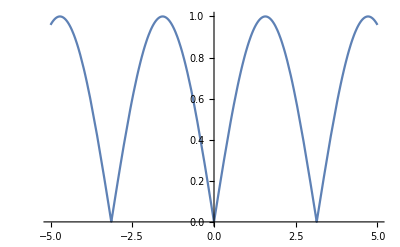

```mathematica
Plot[Abs[Sin[t]], {t,-5,5}]
```

```mathematica
clear n;
clear t;
```

```mathematica
FourierCoefficient[Abs[Sin[x]],x,n]
```

0

5 clear

clear t

1

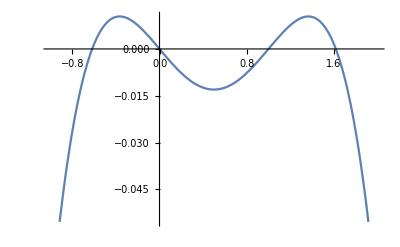

```mathematica
q=1
Plot[-q/24*x^4+q/12*x^3-q/24*x,{x,-1,2}]
```

1

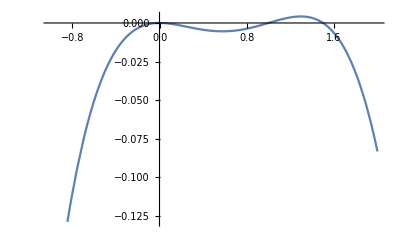

```mathematica
q=1
Plot[-q/24*x^4+5*q/48*x^3-3*q/48*x^2, {x, -1,2}]
```

```mathematica
clear k;
clear L;
clear mA;
clear mb;
mA = {
{1,0,0,1},
{0,1,k,0},
{1,L,Sin[k*L],Cos[k*L]},
{0,0,-k^2*Sin[k*L],-k^2*Cos[k*L]}
};
mb = {
{0},
{0},
{0},
{0}
};
LinearSolve[mA,mb]
```

{{0},{0},{0},{0}}